```mathematica
4
```

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1.00,0.975,0.89]]
```

注释： (*    *)  或  快捷键：  [Alt+/]
	
代码样式：快捷键  [Alt+(1~9)] 或 菜单 Format->Style 中 选择
	
计算： [Shift+Enter]  (!!!!)
	Ctrl+Shift+Enter 计算被选中的表达式

```mathematica
1+1 (*按下shift+enter计算*)
```

2

----------------------------------------------------
数学输入快捷键：
	a^b: a -> [Ctrl+6(^)] -> b
a_b:a -> [Ctrl + -(_) ]-> b
a/b:  a -> [Ctrl+/ ]-> b
(a+b)/(c+d) ：[Ctrl+/ ]-> a+b -> 方向键(↓) -> c+d
	√a：[Ctrl+2(@)] -> a
	a^(1/b)：[Ctrl+2(@)] -> a -> [Ctrl+5(%)] -> b -> 方向键(→)
	注意：输入的数学公式可以以 MathML/LATEX 格式复制到 Office 文档中.

```mathematica
2^3
```

8

```mathematica
2^3
```

8

```mathematica
244/122
```

2

变量赋值:
	a = 3
	注意： 等于是“==”， 赋值是“=”。
查看变量:
	x
	 ?x
	 ??x
下标变量支持，加入两行代码：
	Needs[“Notation`”];
	Symbolize[ParsedBoxWrapper[SubscriptBox[“_”,”_”]]]

```mathematica
a=3
```

3

```mathematica
(*查看变量 a *)?a
```

```mathematica
??a
```

```mathematica
Needs["Notation`"];
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]];    (*强制将下标变成变量名一部分*)
```

```mathematica
Needs[""]
```

```mathematica
Subscript[a, 1]=4  (*带下标的变量赋值*)
```

4

```mathematica
a (*获取变量的值*)
```

3

```mathematica
Subscript[a, 1]
```

4

```mathematica
?Subscript[a, 1]
```

Information[4,LongForm→False]

```mathematica
?Subscript[a, 2]     (*不存在的下标变量*)
```

Information[234,LongForm→False]

----------------------------------------------------
查看所有变量：  (MMA 没有像 MATLAB 那样的变量窗口)
	所有变量代号：  	“Global`*” 	(包含引号)
	? Global`*		: 查看所有变量
	?? Global`*
	
清除所有变量：
	Clear[x] 	 : 清除变量的值，但是不删除变量
	x = .		 : 同上
	Clear[“Global`*”]   ：清除所有变量的值，但是不删除 (别忘了引号)
	
	Remove[x]	: 删除变量
	Remove[“Global`*”]
	
获取上一次数据:	%   (类似计算器的 Ans 键)

```mathematica
Needs["Notation`"];
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
```

```mathematica
a=3
```

3

```mathematica
Subscript[a, 1]=123
```

123

```mathematica
Subscript[a, 2]=234
```

234

```mathematica
%     (*获取上一次数据*)
```

234

```mathematica
??Global`*
```

```mathematica
??Subscript[a, 2]
```

Information[234,LongForm→True]

```mathematica
Clear[a](*清除a*)
```

```mathematica
a
```

a

```mathematica
b = 4
```

4

```mathematica
b = .(*清除b*)
```

```mathematica
b
```

b

```mathematica
c=5
```

5

```mathematica
Clear["Global`*"](*全部清除*)
```

```mathematica
c
```

c

```mathematica
d = 6
```

6

```mathematica
?d
```

```mathematica
Remove[d](*删除 d*)
```

```mathematica
?d
```

Missing[UnknownSymbol,d]

----------------------------------------------------
重置命令行序号：
	-Graphics-

希腊字母、特殊符号：
	Esc  ->  字母/表达式  ->  Esc，如：
	π  : 		Esc -> p -> Esc (或 Tab)
	---------------------------
	°：		Esc -> “deg” -> Esc(或 Tab)
		註：这个符号用于将数字转化为角度制，如 30°
	-----------------------
	∫x^2+x ⅆx： 	Esc-> “intt” -> Esc ->
	∫_■^□ □ⅆ□:           Esc -> “dintt” -> Esc
	∑_(■=□)^□ □:		Esc-> “sumt” -> Esc
	∏_(■=□)^□ □:		“prodt”
	ⅆ:			“dd”
	∂:			“pd”
	⊥:			“perp”(perpendicular 垂直的)
	∨∧⊻¬		“or””and””xor””not”
	·  (乘法点)	“.”
	
常用计算：
	Pi, E		:
	a^b/a^b
	log_b a	:	Log[b, a]
		注意：MMA 中的函数名一律首字母大写，且参数用方括号扩起来
	log_10 a	: 	Log10[a]
	log_e a	: 	Log
	Sin[x], Cos[x], Tan[x], ArcSin[x], ArcCos[x], ArcTan[x]		
		注意：弧度制，且首字母大写，可以在自变量后面加 ° 让它变成角度制
	Sinh[x], Cosh[x], ...
	角度/弧度转换：   Degree(这是一个数==π/180)
		Sin[30 Degree]
		Sin[30 °]
		ArcSin[0.5]   / Degree (*除以 Degree*)
	 a!				:	
	nCr(a, b), nPr(a, b):		
	
	
转换格式：
	-Graphics-     -->	-Graphics-
	
Sin[π/4]

常用命令：

常用函数：

小数输出：
	N[2/3]
	或 表达式后面 加  “//N”
	
	
复数运算：
解一元方程：
解方程组：
解微分方程：
代数式化简：
矩阵运算：

编程：

```mathematica
Pi
```

π

```mathematica
Pi //N(*转化为小数*)
```

3.14159

```mathematica
N[E](*转化为小数*)
```

2.71828

```mathematica
N[E, 30](*转化为小数，保留 30 位*)
```

2.71828182845904523536028747135

```mathematica
Infinity (*无穷*)
```

∞

```mathematica
a= 1+2I(*虚数*)
```

1+2 ⅈ

```mathematica
Re[a](*取实部*)
```

1

```mathematica
Im[a]
```

2

```mathematica
Conjugate[a]
```

1-2 ⅈ

```mathematica
Arg[a] //N(*辐角，弧度*)
```

1.10715

```mathematica
Abs[a]//N
```

2.23607

```mathematica
Log[E](*e 为底的对数*)
```

1

```mathematica
Log[2, 8](*2 为底的对数*)
```

3

```mathematica
GCD[123, 456](*最大公因数*)
```

3

```mathematica
LCM[123, 456](*最小公倍数*)
```

18696

```mathematica
Sin[π/6]  //N
```

0.5

```mathematica
Sin[30 Degree](*角度制*)
```

1/2

```mathematica
Sin [30 °]     //N(*角度制另一种方法*)
```

0.5

```mathematica
??Degree
```

```mathematica
ArcSin[0.5] /Degree(*输出角度*)
```

30.

```mathematica
dms=DMSList[{6, 5, 5}](*度分秒*)
```

{6,5,5}

```mathematica
FromDMS[dms] //N(*度分秒参与计算*)
```

6.08472

```mathematica
DMSString[dms](*输出为度分秒字符串*)
```

6°5'5"

```mathematica
FullSimplify[D[(x^2+2 x)/Log[2,x^3+x^(1/3)], {x}]](*强力化简*)
```

(Log[2] (-6-3 x+(8 (2+x))/(3 (1+x^(8/3)))+2 (1+x) Log[x^(1/3)+x^3]))/(Log[x^(1/3)+x^3]^2)

```mathematica
Remove[x](*删除 x 变量*)
```

```mathematica
F888 = Apart[(6 x^2+5x+3)/((x+1)(x+2)(x+3))](*展开多项式分式*)
```

2/(1+x)-17/(2+x)+21/(3+x)

```mathematica
Apart[x/(x^3-x^2+x-1)]
```

1/(2 (-1+x))+(1-x)/(2 (1+x^2))

```mathematica
F666=Expand[((x+x^2) (x^2+3)^2)/(x-1)](*展开表达式*)
```

(9 x)/(-1+x)+(9 x^2)/(-1+x)+(6 x^3)/(-1+x)+(6 x^4)/(-1+x)+x^5/(-1+x)+x^6/(-1+x)

```mathematica
Series[√(1+x), {x, 0, 10}](*泰勒展开，皮亚诺余项*)
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+(7 x^5)/256-(21 x^6)/1024+(33 x^7)/2048-(429 x^8)/32768+(715 x^9)/65536-(2431 x^10)/262144+O[x]^11

```mathematica
F700=Expand[(x+y)^8](*展开多项式*)
```

x^8+8 x^7 y+28 x^6 y^2+56 x^5 y^3+70 x^4 y^4+56 x^3 y^5+28 x^2 y^6+8 x y^7+y^8

```mathematica
Coefficient[Expand[(x+y)^8], x^2 y^6](*取系数*)
```

28

```mathematica
Series[1/(1-x), {x,0,10}](*级数展开*)
```

1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+O[x]^11

```mathematica
Normal[%](*转为正常的级数*)
```

1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10

```mathematica
Binomial[6, 4](*二项式系数({{n=6}, {k=4}}) *)
```

15

```mathematica
F667=FullSimplify[F666](*强力简化*)
```

(x (1+x) (3+x^2)^2)/(-1+x)

```mathematica
F668=Together[F666](*通分*)
```

(9 x+9 x^2+6 x^3+6 x^4+x^5+x^6)/(-1+x)

```mathematica
Eliminate[{x+5y-z==-1, x-2y+z==3, 3x+8y-z==1}, x](*消元*)
```

2 (-2+z)==7 y

```mathematica
F1 = x^4+2 x^3+3 x^2+2x+5;(*定义一元函数*)
```

```mathematica
?F1
```

```mathematica
D[F1, x](*一阶导数*)
```

2+6 x+6 x^2+4 x^3

```mathematica
D[F1, {x, 2}](*二阶导数*)
```

0

```mathematica
F1′[x]
```

F1′[x]

```mathematica
Integrate[F1, {x, -1, +1}](*积分 ∫_-1^(+1) F1(x)ⅆx *)
```

62/5

```mathematica
∫_-1^(+1) F1ⅆx      (*或者这样*)
```

62/5

```mathematica
Integrate[F1, x](*不定积分*)
```

5 x+x^2+x^3+x^4/2+x^5/5

```mathematica
F1[2](*不可以这样算*)
```

(5+2 x+3 x^2+2 x^3+x^4)[2]

```mathematica
F1/.x->2(*替换表达式中的未知数*)
```

53

```mathematica
F1/.x->t+1
```

5+2 (1+t)+3 (1+t)^2+2 (1+t)^3+(1+t)^4

```mathematica
F2=x^5+x^3+x^3 y^5+y^3+x*y;(*定义二元函数*)
```

```mathematica
?F2
```

```mathematica
Factor[F2](*因式分解*)
```

x^3+x^5+x y+y^3+x^3 y^5

```mathematica
D[F2, x](*偏导数-Graphics-*)
```

3 x^2+5 x^4+y+3 x^2 y^5

```mathematica
D[F2, {x}]/.{x->1,y->2}
```

106

```mathematica
D[F2, {x, 2}](*-Graphics-*)
```

6 x+20 x^3+6 x y^5

```mathematica
D[F2, {x, 2}, {y, 2}](*-Graphics-*)
```

120 x y^3

```mathematica
Integrate[F2,{x,0,1},{y,0,1}]  //N   (*长方形范围内积分-Graphics-*)
```

0.958333

```mathematica
x=5
```

5

```mathematica
F2[[3]](*取出第三项*)
```

x y

```mathematica
F2[[3, 2]](*取出第三项的第二项*)
```

y

```mathematica
F3[x_]= x^2+2x+3;(*如果之前x的值已经确定，则F3将会变成定值，为避免这种情况请使用 := 替代 = *)
```

```mathematica
?F3
```

```mathematica
F3[2](*可以这样算*)
```

11

```mathematica
F3[4]
```

27

```mathematica
F4[x_]:=x^2+2x+3(*使用 := 则不受其影响*)
```

```mathematica
?F4
```

```mathematica
F5=F4[x]
```

3+2 x+x^2

```mathematica
D[F5, x]
```

2+2 x

```mathematica
F6=(x^2+4x)/((x-1)(2x-3))(*定义表达式*)
```

(4 x+x^2)/((-1+x) (-3+2 x))

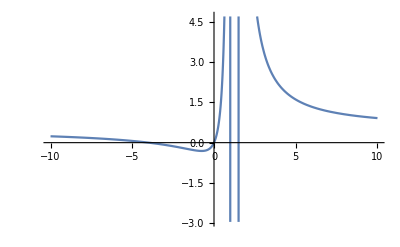

```mathematica
Plot[F6, {x, -10, +10}](*作图*)
```

```mathematica
F6a=Apart[F6](*分解因式*)
```

1/2-5/(-1+x)+33/(2 (-3+2 x))

```mathematica
Together[F6a](*分式合并*)
```

(4 x+x^2)/((-1+x) (-3+2 x))

```mathematica
Simplify[F6a](*化简*)
```

(x (4+x))/((-1+x) (-3+2 x))

```mathematica
FullSimplify[F6a](*强力化简*)
```

(x (4+x))/((-1+x) (-3+2 x))

```mathematica
Limit[F6, x->1](*求极限*)
```

Indeterminate

```mathematica
Limit[F6, x->-Infinity](*趋于负无穷的极限*)
```

1/2

```mathematica
Limit[F6, x->1, Direction->-1]      (*lim_(x->1-) (4 x+x^2)/((-1+x) (-3+2 x)) 左侧极限*)
```

-∞

```mathematica
F7=x^3
```

x^3

```mathematica
Limit[F7, x->Infinity]
```

∞

```mathematica
Solve[x^2+2x+3==0, x](*解方程*)
```

{{x→-1-ⅈ √2},{x→-1+ⅈ √2}}

```mathematica
Solve[x^2+y^2==0, {x, y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-ⅈ x},{y→ⅈ x}}

```mathematica
Reduce[x^2+y^2==0, {x, y}](*解方程，可得出什么时候有解，可解不等式*)
```

y==-ⅈ x||y==ⅈ x

```mathematica
Reduce[x^2+(y+1)^2<1, {x, y}](*解多元不等式*)
```

-1<x<1&&-1-√(1-x^2)<y<-1+√(1-x^2)

```mathematica
FindRoot[Cos[x]+Sin[x]==1, {x, 1}](*解方程近似解，从1展开*)
```

{x→1.5708}

```mathematica
Series[Log[3, x^2+3x], x]
```

Series::sspec: Series specification x is not a list with three elements.

```mathematica
Series[Log[3 x+x^2]/Log[3],{x, 0, 5}] (*在 x==Subscript[x, 0]==0处 展开 级数 到 x^5 项*)
```

(Log[3]+Log[x])/Log[3]+x/(3 Log[3])-x^2/(18 Log[3])+x^3/(81 Log[3])-x^4/(324 Log[3])+x^5/(1215 Log[3])+O[x]^6

```mathematica
Normal.[%]
```

Syntax::sntxf: "Normal." cannot be followed by "[%]".

```mathematica
Integrate[Sin[x y], {x, y}∈Disk[]](*曲线积分*)
```

∫_({x,y}∈Disk[{0,0}]) Sin[x y]

```mathematica
F8[x_]=Piecewise[{{-x, x<0}, {x, 0<=x<=1}, {x^2, x>1}}](*分段函数定义*)
```

Piecewise[{{-x, x<0}, {x, 0≤x≤1}, {x^2, x>1}, {0, True}}]

```mathematica
F8[2]
```

4

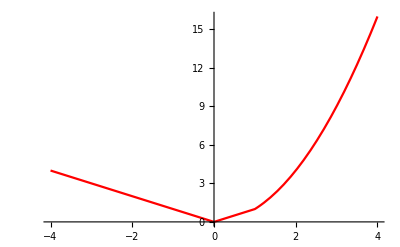

```mathematica
Plot[F8[x], {x, -4, +4}, PlotStyle->Red](*绘制分段函数*)
```

```mathematica
D[F8[x], x](*分段函数求导*)
```

Piecewise[{{-1, x<0}, {1, 0<x<1}, {2 x, x>1}, {Indeterminate, True}}]

```mathematica
SUMUP[x__]:=Plus[x](*变参函数，类似 #define SUMUP(x, ...)*)
```

```mathematica
SUMUP[1, 2, 3, 4]
```

10

```mathematica
Clear[a](*解递推数列表达式，先清除 a 变量*)
```

```mathematica
RSolve[{a[n+2]==5 a[n+1]-6 a[n], a[1]==-1, a[2]==2}, a[n], n]
```

{{a[n]→1/6 (-15 2^n+8 3^n)}}

```mathematica
RSolve[{s[n]==4/3 a[n]-2^(n+1)/3+2/3,s[n+1]-s[n]==a[n+1],a[1]==s[1]},{a[n],s[n]},n]//FullSimplify
(*这里用 s[n+1]-s[n]==a[n+1]的方式声明s[n]是a[n]的和*)
(*-Graphics-*)
```

{{a[n]→-2^n+4^n,s[n]→2/3 (-1+2^n) (-1+2^(1+n))}}

```mathematica
Sum[1/6 (-15 2^n+8 3^n),{n,1,m}]
```

3-5 2^m+2 3^m

```mathematica
sol=DSolve[y'[x]==x, y[x], x](*解微分方程*)
```

{{y[x]→x^2/2+C[1]}}

```mathematica
sol[[1]]
```

{y[x]→x^2/2+C[1]}

```mathematica
f[x_]=y[x]/.sol[[1]]
```

x^2/2+C[1]

```mathematica
sol=DSolve[{y'[x]==x, y[0]==1}, y[x], x]
```

{{y[x]→1/2 (2+x^2)}}

```mathematica
DSolve[y''[x]-2y'[x]+5y[x]==2 ⅇ^x Sin[x]^2, y[x], x]//FullSimplify
```

{{y[x]→-1/4 ⅇ^x (-1+(1-4 C[2]) Cos[2 x]+(x-4 C[1]) Sin[2 x])}}

```mathematica
f[1]
```

y[1]

```mathematica
y[x]
```

y[x]

```mathematica
F2[x_, y_]:=ⅇ^(√(x^4+y^2))(*定义多元函数*)
```

```mathematica
F2dy=D[F2[x, y], y]//FullSimplify(*求偏导数*)
```

(ⅇ^(√(x^4+y^2)) y)/(√(x^4+y^2))

```mathematica
F2dx=D[F2[x, y], x]//FullSimplify
```

(2 ⅇ^(√(x^4+y^2)) x^3)/(√(x^4+y^2))

```mathematica
Dt[F2[x, y] ]//FullSimplify(*求全微分*)
```

(ⅇ^(√(x^4+y^2)) (2 x^3 Dt[x]+y Dt[y]))/(√(x^4+y^2))

```mathematica
Limit[F2dy, {x, y}->{0, 0}](*求多元函数的极限*)
```

Indeterminate

```mathematica
Limit[F2dx,{x,y}->{0,0}]
```

0

```mathematica
Plot3D[{ⅇ^(√(x^4+y^2))}, {x, -1, +1}, {y, -1, +1}, PlotStyle->{Opacity[0.75]}](*绘制三维图形*)
```

-Graphics3D-

注：三维图形查看方法：
按住左键拖动           		    	：旋转
Ctrl + 按住左键上下拖动	：缩放
Shift + 按住左键拖动		：移动
=====================================

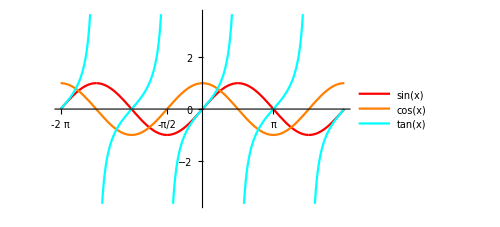

```mathematica
Plot[{Sin[x], Cos[x], Tan[x](*, Sec[x], Csc[x], Cot[x]*)}, {x, -2π, +2π},
PlotLegends->"Expressions"(*旁边的图例*), 
Ticks->{FindDivisions[{-10,10,Pi/2},20],Automatic}(*座标标尺*), 
GridLines->{{0,π/2,π,3 π/2,2 π},{-1,-Sqrt[3]/2,-1/2,0,1/2,Sqrt[3]/2,1}},
PlotStyle->{Red, Orange, Cyan}(*颜色*)]
```

```mathematica
Plot3D[{-(x^2 (2 x+4 x^3) y)/((x^2+x^4)^2)+(2 x y)/(x^2+x^4)}, {x, -1, +1}, {y, -1, +1}, PlotStyle->{Opacity[0.75]}, AxesStyle->Thick, AxesLabel->{x, y, z}, AxesOrigin->{0, 0, 0}, LabelStyle->{12, Normal}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^x+y^y+z^z==2.3,{x,0,1.1},{y,0,1.1},{z,0,1.1}]
```

-Graphics3D-

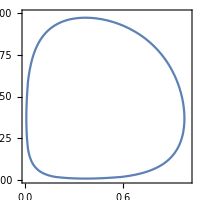

```mathematica
ContourPlot[x^x+y^y==5/3,{x,0,1},{y,0,1},ImageSize->{200,200}](*隐函数图像绘制/解析几何图像*)
```

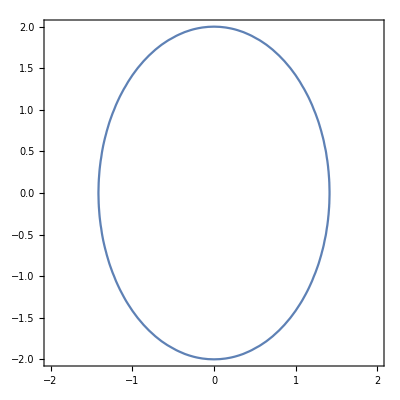

```mathematica
ContourPlot[x^2/2+y^2/4==1, {x, -2, +2}, {y,-2,+2}](*隐函数图像绘制/解析几何图像*)
```

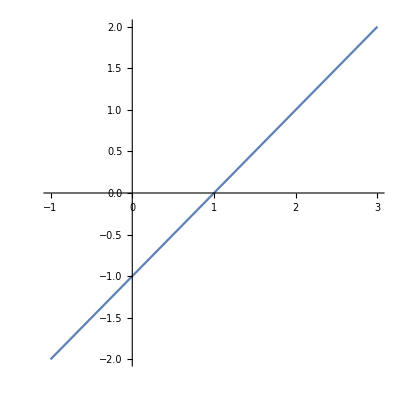

```mathematica
ParametricPlot[{t+1, t},{t, -2, +2}](*参数方程图像，Piecewise[{{x == 1+t, □}, {y == t, □}}]*)
```

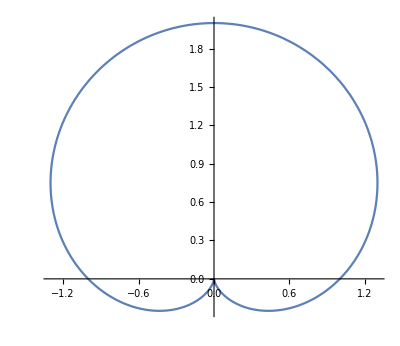

```mathematica
PolarPlot[(1+Sin[θ]), {θ, 0, 2π}](*极座标 r=1+Sin[θ] 星形线*)
```

```mathematica
Manipulate[Show[ParametricPlot[{t+2 Cos[t],1-2 Sin[t]},{t,0,6}],ParametricPlot[#,{θ,0,2π}],Graphics[{Line[{{t,1},#/.θ->0}],Red,PointSize[Large],Point[#/.θ->0]}],PlotRange->{{-2,8},{-1.5,3}},AxesOrigin->{0,0}]&@@{{t+2 Cos[t-θ],1-2 Sin[t-θ]}},{t,0,6}]
```

```mathematica
Manipulate[Show[ParametricPlot[{-1+Cos[2 t]+2 Sin[t],2 Cos[t]-Sin[2 t]},{t,0,2π}],ParametricPlot[{Cos[t]-1,Sin[t]},{t,0,2π}],ParametricPlot[#,{θ,0,2π}],Graphics[{Red,PointSize[Large],Point[#/.θ->0]}],PlotRange->{{-4,2},{-3,3}},AxesOrigin->{0,0}]&@@{{-1+Cos[2 t-θ]+2 Sin[t],2 Cos[t]-Sin[2 t-θ]}},{t,0,2π}]
```

```mathematica
Manipulate[Show[ParametricPlot[{2 t+Cos[t],2-Sin[t]},{t,0,6}],ParametricPlot[#,{θ,0,2π}],Graphics[{Line[{{2 t,2},#/.θ->0}],Red,PointSize[Large],Point[#/.θ->0]}],PlotRange->{{-2,8},{-1.5,3}},AxesOrigin->{0,0}]&@@{{2 t+Cos[t-θ],2-Sin[t-θ]}},{t,0,6}]
```

```mathematica
ParametricPlot3D[{1.16^v Cos[v] (1+Cos[u]),-1.16^v Sin[v] (1+Cos[u]),-2 1.16^v (1+Sin[u])},
			{u,0,2 Pi},{v,-15,6},
			Mesh->None,PlotStyle->{Opacity[0.6],Green},PlotRange->All,PlotPoints->25,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{4+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]},{8+(3+Cos[v]) Cos[u],3+Sin[v],4+(3+Cos[v]) Sin[u]},{12+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]}},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->{{Opacity[0.5],Red},{Opacity[0.5],Green},{Opacity[0.5],Blue}}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[u] Sin[v]+0.05 Cos[20 v],Cos[u] Sin[v]+0.05 Cos[20 u],Cos[v]},{u,-π,π},{v,-π,π},MaxRecursion->4,PlotStyle->{Blue,Specularity[White,10]},Axes->None,Boxed->False,Mesh->None]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[2 u],Sin[2 u],Sqrt[u]+Sin[5 u]/5},{u,0,4 Pi},Mesh->All,PlotStyle->{Pink}]
```

-Graphics3D-

```mathematica
i1=ImageData[-Graphics-];(*傅立叶变换)
i1f=Fourier[i1]
```

{{{234.483+0. ⅈ,4.14929-2.63973 ⅈ,4.14929+2.63973 ⅈ},{6.68291-1.16682 ⅈ,2.26286+1.66827 ⅈ,0.878242-3.18649 ⅈ},209,{6.68291+1.16682 ⅈ,0.878242+3.18649 ⅈ,2.26286-1.66827 ⅈ}},{1},{{1},210,{1}},98,{1},{1},{1}}
 |  |  |  |

```mathematica
i1fi=InverseFourier[i1f]
```

{{{1.+3.1442×10^-18 ⅈ,1.-2.55804×10^-17 ⅈ,1.+2.38269×10^-17 ⅈ},{1.-1.10571×10^-17 ⅈ,1.-1.98135×10^-17 ⅈ,1.+4.43584×10^-18 ⅈ},209,{1.-2.06735×10^-17 ⅈ,1.+3.26149×10^-18 ⅈ,1.+5.80603×10^-17 ⅈ}},{1},{{1},210,{1}},98,{1},{1},{1}}
 |  |  |  |

```mathematica
Image[Abs[i1fi]]
```

-Graphics-

```mathematica
GaussianFilter[-Graphics-, 5] (*对图片进行处理*)
```

-Graphics-

# 线性代数

键盘快捷键：
Ctrl + Enter : 增加列
Ctrl + , 	    :增加行
(1 | 2 | 3)

```mathematica
X={{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}(*矩阵输入({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})*)
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
Det[X](*行列式*)
```

0

```mathematica
Dimensions[X]
```

{3,3}

```mathematica
MatrixForm[X]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
Transpose[X]
```

{{1,4,7},{2,5,8},{3,6,9}}

```mathematica
Xᵀ(*esc->"tr"->esc*)
```

{{1,4,7},{2,5,8},{3,6,9}}

```mathematica
Inverse[X]
```

Inverse::sing: Matrix {{1,2,3},{4,5,6},{7,8,9}} is singular.

Inverse[{{1,2,3},{4,5,6},{7,8,9}}]

```mathematica
Tr[X](*Trace of Martix, 矩阵的迹*)
```

15

```mathematica
Eigenvalues[X](*特征值*)
```

{3/2 (5+√33),3/2 (5-√33),0}

```mathematica
Minors[X]
```

{{-3,-6,-3},{-6,-12,-6},{-3,-6,-3}}

```mathematica
Y=({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})  (*矩阵输入的人性化方式*)
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
Y[[1, 2]] (*取出第一行第二列之元素，双方括号*)
```

2

```mathematica
X2=Table[i/j, {i, 3}, {j, 3}](*根据表达式生成矩阵*)
```

{{1,1/2,1/3},{2,1,2/3},{3,3/2,1}}

```mathematica
X3=Table[Subscript[m, i, j], {i, 5}, {j, 5}];
MatrixForm[X3]
```

(m_(1,1) | m_(1,2) | m_(1,3) | m_(1,4) | m_(1,5)
m_(2,1) | m_(2,2) | m_(2,3) | m_(2,4) | m_(2,5)
m_(3,1) | m_(3,2) | m_(3,3) | m_(3,4) | m_(3,5)
m_(4,1) | m_(4,2) | m_(4,3) | m_(4,4) | m_(4,5)
m_(5,1) | m_(5,2) | m_(5,3) | m_(5,4) | m_(5,5))

```mathematica
X3[[1]]//MatrixForm
```

(m_(1,1)
m_(1,2)
m_(1,3)
m_(1,4)
m_(1,5))

```mathematica
X3[[1, 2]]
```

m_(1,2)

```mathematica
X3[[1]]
```

{m_(1,1),m_(1,2),m_(1,3),m_(1,4),m_(1,5)}

```mathematica
X3[[All, 1]]
```

{m_(1,1),m_(2,1),m_(3,1),m_(4,1),m_(5,1)}

```mathematica
X3[[ {2, 4}]]
```

{{m_(2,1),m_(2,2),m_(2,3),m_(2,4),m_(2,5)},{m_(4,1),m_(4,2),m_(4,3),m_(4,4),m_(4,5)}}

```mathematica
X3[[-1, -1]]
```

m_(5,5)

```mathematica
X3[[2;;4]]//MatrixForm
```

(m_(2,1) | m_(2,2) | m_(2,3) | m_(2,4) | m_(2,5)
m_(3,1) | m_(3,2) | m_(3,3) | m_(3,4) | m_(3,5)
m_(4,1) | m_(4,2) | m_(4,3) | m_(4,4) | m_(4,5))

```mathematica
X3[[All, 2;;4]]//MatrixForm
```

(m_(1,2) | m_(1,3) | m_(1,4)
m_(2,2) | m_(2,3) | m_(2,4)
m_(3,2) | m_(3,3) | m_(3,4)
m_(4,2) | m_(4,3) | m_(4,4)
m_(5,2) | m_(5,3) | m_(5,4))

```mathematica
X3[[1]][[{2, 4}]]//MatrixForm
```

(m_(2,1) | m_(2,2) | m_(2,3) | m_(2,4) | m_(2,5)
m_(4,1) | m_(4,2) | m_(4,3) | m_(4,4) | m_(4,5))

```mathematica
X3[[1]][[All, {2, 4}]]//MatrixForm
```

(m_(1,2) | m_(1,4)
m_(2,2) | m_(2,4)
m_(3,2) | m_(3,4)
m_(4,2) | m_(4,4)
m_(5,2) | m_(5,4))

```mathematica
X3[[1]][[3, 3]]=666
```

666

```mathematica
X3[[1]][[2]]={1, 2, 3, 4, 5}
```

{1,2,3,4,5}

```mathematica
X3[[1]][[{1, 3}]]={a, b, c, d, e}
```

{a,b,c,d,e}

```mathematica
X3[[1]][[{1, 3}]]={{a, b, c, d, e}, {f, g, h, i, j}}
```

{{a,b,c,d,e},{f,g,h,i,j}}

```mathematica
X3[[1]]//MatrixForm
```

(a | b | c | d | e
1 | 2 | 3 | 4 | 5
f | g | h | i | j
m_(4,1) | m_(4,2) | m_(4,3) | m_(4,4) | m_(4,5)
m_(5,1) | m_(5,2) | m_(5,3) | m_(5,4) | m_(5,5))

```mathematica
X3[[1]][[All, 2]]={-1, -2, -3, -4, -5}
```

{-1,-2,-3,-4,-5}

```mathematica
X3//MatrixForm
```

(a | -1 | c | d | e
1 | -2 | 3 | 4 | 5
f | -3 | h | i | j
m_(4,1) | -4 | m_(4,3) | m_(4,4) | m_(4,5)
m_(5,1) | -5 | m_(5,3) | m_(5,4) | m_(5,5))

```mathematica
Drop[X3[[1]], {}, {2, 2}]//MatrixForm
```

(a | c | d | e
1 | 3 | 4 | 5
f | h | i | j
m_(4,1) | m_(4,3) | m_(4,4) | m_(4,5)
m_(5,1) | m_(5,3) | m_(5,4) | m_(5,5))

```mathematica
Drop[X3, {3, 3}]
```

{{a,-1,c,d,e},{1,-2,3,4,5},{m_(4,1),-4,m_(4,3),m_(4,4),m_(4,5)},{m_(5,1),-5,m_(5,3),m_(5,4),m_(5,5)}}

```mathematica
Insert[X3, {x, y, z, α, β}, 3]
```

{{a,-1,c,d,e},{1,-2,3,4,5},{x,y,z,α,β},{f,-3,h,i,j},{m_(4,1),-4,m_(4,3),m_(4,4),m_(4,5)},{m_(5,1),-5,m_(5,3),m_(5,4),m_(5,5)}}

```mathematica
Transpose[Insert[Transpose[X3], {χ, δ, ϵ, ϕ, γ}, 2]]
```

{{a,χ,-1,c,d,e},{1,δ,-2,3,4,5},{f,ϵ,-3,h,i,j},{m_(4,1),ϕ,-4,m_(4,3),m_(4,4),m_(4,5)},{m_(5,1),γ,-5,m_(5,3),m_(5,4),m_(5,5)}}

```mathematica
Minors[X3, {1, 2}]
```

Minors[{{a,-1,c,d,e},{1,-2,3,4,5},{f,-3,h,i,j},{m_(4,1),-4,m_(4,3),m_(4,4),m_(4,5)},{m_(5,1),-5,m_(5,3),m_(5,4),m_(5,5)}},{1,2}]

```mathematica
Tr[X3](**)
```

```mathematica
Subscript[m, 1,1]+Subscript[m, 2,2]+Subscript[m, 3,3]+Subscript[m, 4,4](*对角线元素相加 Diagonal elements*)
```

```mathematica
X4=Table[2(i-1)+j, {i, 2}, {j, 3}]
```

{{1,2,3},{3,4,5}}

```mathematica
PadLeft[X4, {4, 4}]
```

{{0,0,0,0},{0,0,0,0},{0,1,2,3},{0,3,4,5}}

```mathematica
PadRight[X4, {4, 4}]
```

{{1,2,3,0},{3,4,5,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Transpose[X4]
```

{{1,3},{2,4},{3,5}}

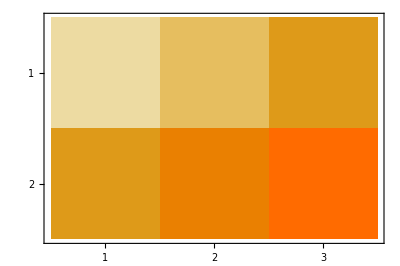

```mathematica
MatrixPlot[X4]
```

```mathematica
m=IdentityMatrix[5]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
m[[1]]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
A3=DiagonalMatrix[Table[RandomReal[{-10,+10}],5]];
MatrixForm[A3](*生成对角矩阵，且用随机数填充之*)
```

(3.55259 | 0. | 0. | 0. | 0.
0. | -2.85255 | 0. | 0. | 0.
0. | 0. | 3.90752 | 0. | 0.
0. | 0. | 0. | -3.88796 | 0.
0. | 0. | 0. | 0. | 4.80884)

```mathematica
vect={1, 2, 3}
```

{1,2,3}

```mathematica
Dimensions[vect]
```

{3}

```mathematica
ma1=({{1, 2, 3}, {4, 5, 6}, {8, 5, 3}})
```

{{1,2,3},{4,5,6},{8,5,3}}

```mathematica
Det[ma1]
```

-3

```mathematica
ma1ᵀ//MatrixForm
```

(1 | 4 | 8
2 | 5 | 5
3 | 6 | 3)

```mathematica
Transpose[ma1]
```

{{1,4,8},{2,5,5},{3,6,3}}

```mathematica
Inverse[ma1]//MatrixForm
```

(5 | -3 | 1
-12 | 7 | -2
20/3 | -11/3 | 1)

```mathematica
ma2=Table[i+j, {i, 3}, {j, 3}];
MatrixForm[ma2]
```

(2 | 3 | 4
3 | 4 | 5
4 | 5 | 6)

```mathematica
Det[ma2]
```

0

```mathematica
ma1//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
8 | 5 | 3)

```mathematica
ma2//MatrixForm
```

(2 | 3 | 4
3 | 4 | 5
4 | 5 | 6)

```mathematica
ma1*ma2//MatrixForm(*矩阵的数乘*)
```

(2 | 6 | 12
12 | 20 | 30
32 | 25 | 18)

```mathematica
ma1.ma2//MatrixForm(*矩阵的矩阵乘积*)
```

(20 | 26 | 32
47 | 62 | 77
43 | 59 | 75)

```mathematica
ma1/ma2//MatrixForm(*矩阵的数除*)
```

(1/2 | 2/3 | 3/4
4/3 | 5/4 | 6/5
2 | 1 | 1/2)

```mathematica
RowReduce[ma1]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
MatrixRank[ma2](*矩阵的秩*)
```

2

```mathematica
MatrixAdjoint[m_]:=Inverse[m]*Det[m](*伴随矩阵*)
```

```mathematica
MatrixAdjoint[ma1]//MatrixForm
```

(-15 | 9 | -3
36 | -21 | 6
-20 | 11 | -3)

```mathematica
γ=Table[RandomReal[{-10, +10}], {i, 10}, {j, 1}];
MatrixForm[γ]
```

(6.68903
-0.919479
1.5937
-2.89493
-5.34409
-7.26432
-2.64156
2.22053
1.70022
-7.90888)

```mathematica
δ=Table[RandomReal[{-10, +10}], {i,10}, {j, 1}]
```

{{5.49359},{-7.23711},{5.03691},{1.04492},{0.484549},{1.04436},{2.83379},{3.00855},{-2.8023},{4.41543}}

```mathematica
γᵀ.δ//MatrixForm
```

(139.633)

```mathematica
γ.δᵀ//MatrixForm
```

(19.587 | -25.8034 | 17.9587 | 3.7256 | 1.72762 | 3.72357 | 10.1037 | 10.7268 | -9.9914 | 15.7429
-45.7355 | 60.2508 | -41.9336 | -8.69926 | -4.03399 | -8.69452 | -23.592 | -25.0469 | 23.3299 | -36.7595
54.5504 | -71.8633 | 50.0157 | 10.3759 | 4.81149 | 10.3703 | 28.1391 | 29.8744 | -27.8264 | 43.8444
-13.7045 | 18.0539 | -12.5652 | -2.6067 | -1.20877 | -2.60527 | -7.06925 | -7.50521 | 6.9907 | -11.0148
51.1668 | -67.4058 | 46.9134 | 9.73233 | 4.51304 | 9.72703 | 26.3937 | 28.0214 | -26.1004 | 41.1249
-39.8253 | 52.4648 | -36.5147 | -7.57509 | -3.51269 | -7.57096 | -20.5433 | -21.8102 | 20.3151 | -32.0093
2.62206 | -3.45424 | 2.40409 | 0.498737 | 0.231273 | 0.498465 | 1.35255 | 1.43597 | -1.33752 | 2.10746
33.5697 | -44.2239 | 30.7791 | 6.38523 | 2.96093 | 6.38175 | 17.3165 | 18.3844 | -17.1241 | 26.9814
4.96507 | -6.54085 | 4.55232 | 0.944395 | 0.437931 | 0.94388 | 2.56116 | 2.71911 | -2.5327 | 3.99063
-2.18966 | 2.8846 | -2.00763 | -0.41649 | -0.193133 | -0.416263 | -1.1295 | -1.19916 | 1.11695 | -1.75992)

```mathematica
MatrixRank[γ.δᵀ]
```

1

```mathematica
A2=({{0, 1, 0}, {0, 0, 1}, {0, 0, 0}})
```

{{0,1,0},{0,0,1},{0,0,0}}

```mathematica
MatrixPower[A2, 4]//MatrixForm (*矩阵的幂*)
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
({{9, 7, 6, 3, 5}, {18, 14, 12, 6, 10}, {27, 21, 18, 9, 15}, {36, 28, 24, 12, 20}, {45, 35, 30, 15, 25}}).({{2, 0, 0, 0, 0}, {0, 2, 0, 0, 0}, {0, 0, 2, 0, 0}, {0, 0, 0, 2, 0}, {0, 0, 0, 0, 2}})//MatrixForm
```

(18 | 14 | 12 | 6 | 10
36 | 28 | 24 | 12 | 20
54 | 42 | 36 | 18 | 30
72 | 56 | 48 | 24 | 40
90 | 70 | 60 | 30 | 50)

```mathematica
IdentityMatrix[5].({{18, 14, 12, 6, 10}, {36, 28, 24, 12, 20}, {54, 42, 36, 18, 30}, {72, 56, 48, 24, 40}, {90, 70, 60, 30, 50}}).IdentityMatrix[5]//MatrixForm
```

(18 | 14 | 12 | 6 | 10
36 | 28 | 24 | 12 | 20
54 | 42 | 36 | 18 | 30
72 | 56 | 48 | 24 | 40
90 | 70 | 60 | 30 | 50)

```mathematica
B1=DiagonalMatrix[{1, 2, 3}]+DiagonalMatrix[{4, 5}, 1];
B1//MatrixForm
```

(1 | 4 | 0
0 | 2 | 5
0 | 0 | 3)

```mathematica
UnitVector[4, 2](*The unit vector in the direction 2 in four dimensions:*)
```

{0,1,0,0}

```mathematica
RowReduce[({{1, 5, -1, -1}, {1, -2, 1, 3}, {3, 6, 1, 1}})](*行阶梯最简型*)//MatrixForm
```

(1 | 0 | 0 | 11/5
0 | 1 | 0 | -4/5
0 | 0 | 1 | -4/5)

```mathematica
RowReduce[({{1, 5, -1, -1}, {1, -2, 1, 3}, {3, 8, -1, 1}})]//MatrixForm
```

(1 | 0 | 3/7 | 13/7
0 | 1 | -2/7 | -4/7
0 | 0 | 0 | 0)

```mathematica
A3=({{1, 0, 1}, {0, 1, 0}, {0, 0, 1}})
```

{{1,0,1},{0,1,0},{0,0,1}}

```mathematica
Eigenvalues[A3]
```

{1,1,1}

```mathematica
Eigenvectors[A3]
```

{{0,1,0},{1,0,0},{0,0,0}}

```mathematica
Eigenvectors[{A3, 1}]
```

Eigenvectors::matrix: Argument 1 at position 2 is not a non-empty rectangular matrix.

Eigenvectors[{{{1,0,1},{0,1,0},{0,0,1}},1}]

```mathematica
Eigensystem[A3]
```

{{1,1,1},{{0,1,0},{1,0,0},{0,0,0}}}

```mathematica
A4=({{0, 0, 1}, {0, 1, 0}, {1, 0, 0}})
```

{{0,0,1},{0,1,0},{1,0,0}}

```mathematica
Eigensystem[A4]//MatrixForm
```

(-1 | 1 | 1
{-1,0,1} | {1,0,1} | {0,1,0})

```mathematica
A5=({{1, 1}, {0, 1}})
```

{{1,1},{0,1}}

```mathematica
{v1, v2}=Eigenvectors[A5]
```

{{1,0},{0,0}}

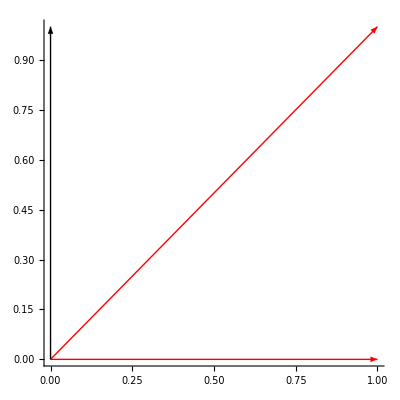

```mathematica
Graphics[{ {  Red, Arrow[{{0, 0}, v1}]       },
		 { Red, Arrow[{{0, 0}, A5.{0, 1}}]},
		 { Thick, Arrow[{{0, 0}, {0, 1}}]}
			}, Axes->True]
```

```mathematica
R
```

```mathematica
Graphics[{{Thick,Arrow[{{0,0},v1}]},{Red,Arrow[{{0,0},m.v1}]}},Axes->True]
```

# 统计

```mathematica
data={1, 2, 3, 4, 5, 6, 7, 8, 100}(*一组数据*)
```

{1,2,3,4,5,6,7,8,100}

```mathematica
Mean[data] //N(*平均数*)
```

15.1111

```mathematica
Median[data] //N(*中位数*)
```

5.

```mathematica
GeometricMean[data]//N(*几何平均*)
```

5.41934

```mathematica
Variance[data] //N(*样本方差-Graphics-*)
```

1018.61

```mathematica
VarianceMLE[data] //N(*总体方差-Graphics-*)
```

VarianceMLE[{1.,2.,3.,4.,5.,6.,7.,8.,100.}]

```mathematica
StandardDeviation[data] //N(*样本标准差*)
```

31.9157

```mathematica
??Global`*
```